```mathematica
Clear[f,theta]
("Eddington factor")
ChiEdd[f_]=(5+6*f^2-2*f^3+6*f**4)/15
```

Eddington factor

1/15 (5+6 f^2-2 f^3+6 f**4)

```mathematica
("Hydrodynamical Variables")
Pxx[Ene_,Fx_,Fy_]=(1-ChiEdd[Sqrt[Fx*Fx+Fy*Fy]/Ene])/2*Ene + (3*ChiEdd[Sqrt[Fx*Fx+Fy*Fy]/Ene]-1)/2*Ene*Fx*Fx/(Fx*Fx+Fy*Fy)
Pxy[Ene_,Fx_,Fy_]= (3*ChiEdd[Sqrt[Fx*Fx+Fy*Fy]/Ene]-1)/2*Ene*Fx*Fy/(Fx*Fx+Fy*Fy)
DEDPxx[Ene_,Fx_,Fy_]=Simplify[D[Pxx[Ene,Fx,Fy],Ene]]
DFxDPxx[Ene_,Fx_,Fy_]=Simplify[D[Pxx[Ene,Fx,Fy],Fx]]
DFyDPxx[Ene_,Fx_,Fy_]=Simplify[D[Pxx[Ene,Fx,Fy],Fy]]
DEDPxy[Ene_,Fx_,Fy_]=Simplify[D[Pxy[Ene,Fx,Fy],Ene]]
DFxDPxy[Ene_,Fx_,Fy_]=Simplify[D[Pxy[Ene,Fx,Fy],Fx]]
DFyDPxy[Ene_,Fx_,Fy_]=Simplify[D[Pxy[Ene,Fx,Fy],Fy]]
DEDPxx[Ene_,Fx_,Fy_]=Simplify[D[Pxx[Ene,Fx,Fy],Ene]]
DFxDPxx[Ene_,Fx_,Fy_]=Simplify[D[Pxx[Ene,Fx,Fy],Fx]]
DFyDPxx[Ene_,Fx_,Fy_]=Simplify[D[Pxx[Ene,Fx,Fy],Fy]]
DEDPxy[Ene_,Fx_,Fy_]=Simplify[D[Pxy[Ene,Fx,Fy],Ene]]
DFxDPxy[Ene_,Fx_,Fy_]=Simplify[D[Pxy[Ene,Fx,Fy],Fx]]
DFyDPxy[Ene_,Fx_,Fy_]=Simplify[D[Pxy[Ene,Fx,Fy],Fy]]
```

Hydrodynamical Variables

1/2 Ene (1+1/15 (-5-(6 (Fx^2+Fy^2))/Ene^2+(2 (Fx^2+Fy^2)^(3/2))/Ene^3-6 (√(Fx^2+Fy^2))/Ene**4))+(Ene Fx^2 (-1+1/5 (5+(6 (Fx^2+Fy^2))/Ene^2-(2 (Fx^2+Fy^2)^(3/2))/Ene^3+6 (√(Fx^2+Fy^2))/Ene**4)))/(2 (Fx^2+Fy^2))

(Ene Fx Fy (-1+1/5 (5+(6 (Fx^2+Fy^2))/Ene^2-(2 (Fx^2+Fy^2)^(3/2))/Ene^3+6 (√(Fx^2+Fy^2))/Ene**4)))/(2 (Fx^2+Fy^2))

1/(15 Ene^3 (Fx^2+Fy^2))(5 Ene^3 Fx^2-6 Ene Fx^4+5 Ene^3 Fy^2-3 Ene Fx^2 Fy^2+3 Ene Fy^4+4 Fx^4 √(Fx^2+Fy^2)+2 Fx^2 Fy^2 √(Fx^2+Fy^2)-2 Fy^4 √(Fx^2+Fy^2)+3 Ene^4 (2 Fx^2-Fy^2) (-(√(Fx^2+Fy^2))/Ene^2)**4+3 Ene^4 (2 Fx^2-Fy^2) (√(Fx^2+Fy^2))/Ene**0+6 Ene^3 Fx^2 (√(Fx^2+Fy^2))/Ene**4-3 Ene^3 Fy^2 (√(Fx^2+Fy^2))/Ene**4)

1/(5 Ene^2 (Fx^2+Fy^2)^2)(Ene^3 (2 Fx^4+Fx^2 Fy^2-Fy^4) Fx/(Ene √(Fx^2+Fy^2))**4+Ene^3 (2 Fx^4+Fx^2 Fy^2-Fy^4) (√(Fx^2+Fy^2))/Ene**0+Fx (-(Fx^2+Fy^2) (-4 Ene (Fx^2+Fy^2)+√(Fx^2+Fy^2) (2 Fx^2+Fy^2))+6 Ene^3 Fy^2 (√(Fx^2+Fy^2))/Ene**4))

1/(5 Ene^2 (Fx^2+Fy^2)^2)(-2 Ene Fx^4 Fy-4 Ene Fx^2 Fy^3-2 Ene Fy^5+Fx^2 Fy^3 √(Fx^2+Fy^2)+Fy^5 √(Fx^2+Fy^2)+Ene^3 (2 Fx^4+Fx^2 Fy^2-Fy^4) Fy/(Ene √(Fx^2+Fy^2))**4+Ene^3 (2 Fx^4+Fx^2 Fy^2-Fy^4) (√(Fx^2+Fy^2))/Ene**0-6 Ene^3 Fx^2 Fy (√(Fx^2+Fy^2))/Ene**4)

1/(5 Ene^3 (Fx^2+Fy^2))Fx Fy (-3 Ene Fx^2-3 Ene Fy^2+2 Fx^2 √(Fx^2+Fy^2)+2 Fy^2 √(Fx^2+Fy^2)+3 Ene^4 (-(√(Fx^2+Fy^2))/Ene^2)**4+3 Ene^4 (√(Fx^2+Fy^2))/Ene**0+3 Ene^3 (√(Fx^2+Fy^2))/Ene**4)

1/(5 Ene^2 (Fx^2+Fy^2)^2)Fy (3 Ene Fx^4+6 Ene Fx^2 Fy^2+3 Ene Fy^4-2 Fx^4 √(Fx^2+Fy^2)-3 Fx^2 Fy^2 √(Fx^2+Fy^2)-Fy^4 √(Fx^2+Fy^2)+3 Ene^3 Fx (Fx^2+Fy^2) Fx/(Ene √(Fx^2+Fy^2))**4+3 Ene^3 Fx (Fx^2+Fy^2) (√(Fx^2+Fy^2))/Ene**0-3 Ene^3 Fx^2 (√(Fx^2+Fy^2))/Ene**4+3 Ene^3 Fy^2 (√(Fx^2+Fy^2))/Ene**4)

1/(5 Ene^2 (Fx^2+Fy^2)^2)Fx (3 Ene Fx^4+6 Ene Fx^2 Fy^2+3 Ene Fy^4-Fx^4 √(Fx^2+Fy^2)-3 Fx^2 Fy^2 √(Fx^2+Fy^2)-2 Fy^4 √(Fx^2+Fy^2)+3 Ene^3 Fy (Fx^2+Fy^2) Fy/(Ene √(Fx^2+Fy^2))**4+3 Ene^3 Fy (Fx^2+Fy^2) (√(Fx^2+Fy^2))/Ene**0+3 Ene^3 Fx^2 (√(Fx^2+Fy^2))/Ene**4-3 Ene^3 Fy^2 (√(Fx^2+Fy^2))/Ene**4)

1/(15 Ene^3 (Fx^2+Fy^2))(5 Ene^3 Fx^2-6 Ene Fx^4+5 Ene^3 Fy^2-3 Ene Fx^2 Fy^2+3 Ene Fy^4+4 Fx^4 √(Fx^2+Fy^2)+2 Fx^2 Fy^2 √(Fx^2+Fy^2)-2 Fy^4 √(Fx^2+Fy^2)+3 Ene^4 (2 Fx^2-Fy^2) (-(√(Fx^2+Fy^2))/Ene^2)**4+3 Ene^4 (2 Fx^2-Fy^2) (√(Fx^2+Fy^2))/Ene**0+6 Ene^3 Fx^2 (√(Fx^2+Fy^2))/Ene**4-3 Ene^3 Fy^2 (√(Fx^2+Fy^2))/Ene**4)

1/(5 Ene^2 (Fx^2+Fy^2)^2)(Ene^3 (2 Fx^4+Fx^2 Fy^2-Fy^4) Fx/(Ene √(Fx^2+Fy^2))**4+Ene^3 (2 Fx^4+Fx^2 Fy^2-Fy^4) (√(Fx^2+Fy^2))/Ene**0+Fx (-(Fx^2+Fy^2) (-4 Ene (Fx^2+Fy^2)+√(Fx^2+Fy^2) (2 Fx^2+Fy^2))+6 Ene^3 Fy^2 (√(Fx^2+Fy^2))/Ene**4))

1/(5 Ene^2 (Fx^2+Fy^2)^2)(-2 Ene Fx^4 Fy-4 Ene Fx^2 Fy^3-2 Ene Fy^5+Fx^2 Fy^3 √(Fx^2+Fy^2)+Fy^5 √(Fx^2+Fy^2)+Ene^3 (2 Fx^4+Fx^2 Fy^2-Fy^4) Fy/(Ene √(Fx^2+Fy^2))**4+Ene^3 (2 Fx^4+Fx^2 Fy^2-Fy^4) (√(Fx^2+Fy^2))/Ene**0-6 Ene^3 Fx^2 Fy (√(Fx^2+Fy^2))/Ene**4)

1/(5 Ene^3 (Fx^2+Fy^2))Fx Fy (-3 Ene Fx^2-3 Ene Fy^2+2 Fx^2 √(Fx^2+Fy^2)+2 Fy^2 √(Fx^2+Fy^2)+3 Ene^4 (-(√(Fx^2+Fy^2))/Ene^2)**4+3 Ene^4 (√(Fx^2+Fy^2))/Ene**0+3 Ene^3 (√(Fx^2+Fy^2))/Ene**4)

1/(5 Ene^2 (Fx^2+Fy^2)^2)Fy (3 Ene Fx^4+6 Ene Fx^2 Fy^2+3 Ene Fy^4-2 Fx^4 √(Fx^2+Fy^2)-3 Fx^2 Fy^2 √(Fx^2+Fy^2)-Fy^4 √(Fx^2+Fy^2)+3 Ene^3 Fx (Fx^2+Fy^2) Fx/(Ene √(Fx^2+Fy^2))**4+3 Ene^3 Fx (Fx^2+Fy^2) (√(Fx^2+Fy^2))/Ene**0-3 Ene^3 Fx^2 (√(Fx^2+Fy^2))/Ene**4+3 Ene^3 Fy^2 (√(Fx^2+Fy^2))/Ene**4)

1/(5 Ene^2 (Fx^2+Fy^2)^2)Fx (3 Ene Fx^4+6 Ene Fx^2 Fy^2+3 Ene Fy^4-Fx^4 √(Fx^2+Fy^2)-3 Fx^2 Fy^2 √(Fx^2+Fy^2)-2 Fy^4 √(Fx^2+Fy^2)+3 Ene^3 Fy (Fx^2+Fy^2) Fy/(Ene √(Fx^2+Fy^2))**4+3 Ene^3 Fy (Fx^2+Fy^2) (√(Fx^2+Fy^2))/Ene**0+3 Ene^3 Fx^2 (√(Fx^2+Fy^2))/Ene**4-3 Ene^3 Fy^2 (√(Fx^2+Fy^2))/Ene**4)

```mathematica
("determinant")
CharEq[x_,Ene_,Fx_,Fy_]=Simplify[x*(x-DFxDPxx[Ene,Fx,Fy])*(x-DFyDPxy[Ene,Fx,Fy])-DEDPxy[Ene,Fx,Fy]*DFyDPxx[Ene,Fx,Fy]-x*DFyDPxx[Ene,Fx,Fy]*DFxDPxy[Ene,Fx,Fy]-(x-DFyDPxy[Ene,Fx,Fy])*DEDPxx[Ene,Fx,Fy]]
("determinant when f is parallel to transport direction")
CharEq2[x_,Ene_,Fx_,Fy_]=Simplify[x*(x-DFxDPxx[Ene,Fx,Fy])-DEDPxx[Ene,Fx,Fy]]
```

determinant

1/75 (-1/(Ene^5 (Fx^2+Fy^2)^3)3 Fx Fy (-3 Ene Fx^2-3 Ene Fy^2+2 Fx^2 √(Fx^2+Fy^2)+2 Fy^2 √(Fx^2+Fy^2)+3 Ene^4 (-(√(Fx^2+Fy^2))/Ene^2)**4+3 Ene^4 (√(Fx^2+Fy^2))/Ene**0+3 Ene^3 (√(Fx^2+Fy^2))/Ene**4) (-2 Ene Fx^4 Fy-4 Ene Fx^2 Fy^3-2 Ene Fy^5+Fx^2 Fy^3 √(Fx^2+Fy^2)+Fy^5 √(Fx^2+Fy^2)+Ene^3 (2 Fx^4+Fx^2 Fy^2-Fy^4) Fy/(Ene √(Fx^2+Fy^2))**4+Ene^3 (2 Fx^4+Fx^2 Fy^2-Fy^4) (√(Fx^2+Fy^2))/Ene**0-6 Ene^3 Fx^2 Fy (√(Fx^2+Fy^2))/Ene**4)+1/(Ene^4 (Fx^2+Fy^2)^4)3 Fy x (3 Ene Fx^4+6 Ene Fx^2 Fy^2+3 Ene Fy^4-2 Fx^4 √(Fx^2+Fy^2)-3 Fx^2 Fy^2 √(Fx^2+Fy^2)-Fy^4 √(Fx^2+Fy^2)+3 Ene^3 Fx (Fx^2+Fy^2) Fx/(Ene √(Fx^2+Fy^2))**4+3 Ene^3 Fx (Fx^2+Fy^2) (√(Fx^2+Fy^2))/Ene**0-3 Ene^3 Fx^2 (√(Fx^2+Fy^2))/Ene**4+3 Ene^3 Fy^2 (√(Fx^2+Fy^2))/Ene**4) (Ene^3 (-2 Fx^4-Fx^2 Fy^2+Fy^4) Fy/(Ene √(Fx^2+Fy^2))**4+Ene^3 (-2 Fx^4-Fx^2 Fy^2+Fy^4) (√(Fx^2+Fy^2))/Ene**0+Fy ((Fx^2+Fy^2) (-Fy^2 √(Fx^2+Fy^2)+2 Ene (Fx^2+Fy^2))+6 Ene^3 Fx^2 (√(Fx^2+Fy^2))/Ene**4))-1/(Ene^3 (Fx^2+Fy^2))5 (5 Ene^3 Fx^2-6 Ene Fx^4+5 Ene^3 Fy^2-3 Ene Fx^2 Fy^2+3 Ene Fy^4+4 Fx^4 √(Fx^2+Fy^2)+2 Fx^2 Fy^2 √(Fx^2+Fy^2)-2 Fy^4 √(Fx^2+Fy^2)+3 Ene^4 (2 Fx^2-Fy^2) (-(√(Fx^2+Fy^2))/Ene^2)**4+3 Ene^4 (2 Fx^2-Fy^2) (√(Fx^2+Fy^2))/Ene**0+6 Ene^3 Fx^2 (√(Fx^2+Fy^2))/Ene**4-3 Ene^3 Fy^2 (√(Fx^2+Fy^2))/Ene**4) (x-1/(5 Ene^2 (Fx^2+Fy^2)^2)Fx (3 Ene Fx^4+6 Ene Fx^2 Fy^2+3 Ene Fy^4-Fx^4 √(Fx^2+Fy^2)-3 Fx^2 Fy^2 √(Fx^2+Fy^2)-2 Fy^4 √(Fx^2+Fy^2)+3 Ene^3 Fy (Fx^2+Fy^2) Fy/(Ene √(Fx^2+Fy^2))**4+3 Ene^3 Fy (Fx^2+Fy^2) (√(Fx^2+Fy^2))/Ene**0+3 Ene^3 Fx^2 (√(Fx^2+Fy^2))/Ene**4-3 Ene^3 Fy^2 (√(Fx^2+Fy^2))/Ene**4))+75 x (x-1/(5 Ene^2 (Fx^2+Fy^2)^2)Fx (3 Ene Fx^4+6 Ene Fx^2 Fy^2+3 Ene Fy^4-Fx^4 √(Fx^2+Fy^2)-3 Fx^2 Fy^2 √(Fx^2+Fy^2)-2 Fy^4 √(Fx^2+Fy^2)+3 Ene^3 Fy (Fx^2+Fy^2) Fy/(Ene √(Fx^2+Fy^2))**4+3 Ene^3 Fy (Fx^2+Fy^2) (√(Fx^2+Fy^2))/Ene**0+3 Ene^3 Fx^2 (√(Fx^2+Fy^2))/Ene**4-3 Ene^3 Fy^2 (√(Fx^2+Fy^2))/Ene**4)) (x+1/(5 Ene^2 (Fx^2+Fy^2)^2)(Ene^3 (-2 Fx^4-Fx^2 Fy^2+Fy^4) Fx/(Ene √(Fx^2+Fy^2))**4+Ene^3 (-2 Fx^4-Fx^2 Fy^2+Fy^4) (√(Fx^2+Fy^2))/Ene**0+Fx ((Fx^2+Fy^2) (-4 Ene (Fx^2+Fy^2)+√(Fx^2+Fy^2) (2 Fx^2+Fy^2))-6 Ene^3 Fy^2 (√(Fx^2+Fy^2))/Ene**4))))

determinant when f is parallel to transport direction

1/(15 Ene^3 (Fx^2+Fy^2))(-5 Ene^3 Fx^2+6 Ene Fx^4-5 Ene^3 Fy^2+3 Ene Fx^2 Fy^2-3 Ene Fy^4-4 Fx^4 √(Fx^2+Fy^2)-2 Fx^2 Fy^2 √(Fx^2+Fy^2)+2 Fy^4 √(Fx^2+Fy^2)+3 Ene^4 (-2 Fx^2+Fy^2) (-(√(Fx^2+Fy^2))/Ene^2)**4+3 Ene^4 (-2 Fx^2+Fy^2) (√(Fx^2+Fy^2))/Ene**0-6 Ene^3 Fx^2 (√(Fx^2+Fy^2))/Ene**4+3 Ene^3 Fy^2 (√(Fx^2+Fy^2))/Ene**4)+x (x+1/(5 Ene^2 (Fx^2+Fy^2)^2)(Ene^3 (-2 Fx^4-Fx^2 Fy^2+Fy^4) Fx/(Ene √(Fx^2+Fy^2))**4+Ene^3 (-2 Fx^4-Fx^2 Fy^2+Fy^4) (√(Fx^2+Fy^2))/Ene**0+Fx ((Fx^2+Fy^2) (-4 Ene (Fx^2+Fy^2)+√(Fx^2+Fy^2) (2 Fx^2+Fy^2))-6 Ene^3 Fy^2 (√(Fx^2+Fy^2))/Ene**4)))

```mathematica
("characteristic speed when f is parallel to the transport direction")
CharpN[f_]=Simplify[(DFxDPxx[1,f,0]+Sqrt[DFxDPxx[1,f,0]*DFxDPxx[1,f,0]+4*DEDPxx[1,f,0]])/2,Element[f,Reals]]
CharmN[f_]=Simplify[(DFxDPxx[1,f,0]-Sqrt[DFxDPxx[1,f,0]*DFxDPxx[1,f,0]+4*DEDPxx[1,f,0]])/2,Element[f,Reals]]
CharoN[f_] =Simplify[DFyDPxy[1,f,0],Element[f,Reals]]
Plot[{CharpN[f],CharmN[f],CharoN[f]},{f,0.0,1.0},AxesLabel->{"|f|","λ"}]
Export["m1normal.eps",%]
```

characteristic speed when f is parallel to the transport direction

1/15 (6 f-3 f Abs[f]+3 f/Abs[f]**4+3 Abs[f]**0+√3 √(25-18 f^2+3 f^4+8 Abs[f]^3+3 (f/Abs[f]**4)^2+30 (-Abs[f])**4+30 Abs[f]**0+12 f Abs[f]**0+3 (Abs[f]**0)^2+6 f/Abs[f]**4 (2 f+Abs[f]**0)-6 f Abs[f] (f/Abs[f]**4+Abs[f]**0)+30 Abs[f]**4))

1/15 (6 f-3 f Abs[f]+3 f/Abs[f]**4+3 Abs[f]**0-√3 √(25-18 f^2+3 f^4+8 Abs[f]^3+3 (f/Abs[f]**4)^2+30 (-Abs[f])**4+30 Abs[f]**0+12 f Abs[f]**0+3 (Abs[f]**0)^2+6 f/Abs[f]**4 (2 f+Abs[f]**0)-6 f Abs[f] (f/Abs[f]**4+Abs[f]**0)+30 Abs[f]**4))

-(Abs[f]^3-3 (f^2+Abs[f]**4))/(5 f)

-Graphics-

m1normal.eps

-Graphics-

m1normal.eps

```mathematica
("characteristic speed when f is perpendicular to the transport direction")
CharPp[f_] =Simplify[(DFyDPxy[1,0,f]+DFxDPxx[1,0,f] +Sqrt[(DFyDPxy[1,0,f]+DFxDPxx[1,0,f] )^2-4*(-DFyDPxx[1,0,f]*DFxDPxy[1,0,f] -DEDPxx[1,0,f] +DFyDPxy[1,0,f]*DFxDPxx[1,0,f])])/2]
CharPm[f_] =Simplify[(DFyDPxy[1,0,f]+DFxDPxx[1,0,f] -Sqrt[(DFyDPxy[1,0,f]+DFxDPxx[1,0,f] )^2-4*(-DFyDPxx[1,0,f]*DFxDPxy[1,0,f] -DEDPxx[1,0,f] +DFyDPxy[1,0,f]*DFxDPxx[1,0,f])])/2]
```

characteristic speed when f is perpendicular to the transport direction

characteristic speed when f is perpendicular to the transport direction

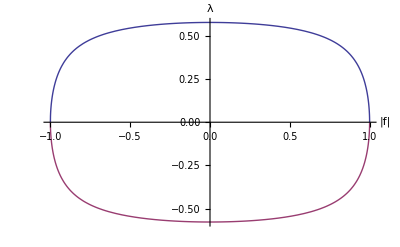

m1papend.eps

```mathematica
Plot[ {CharPp[f] ,CharPm[f]}, {f,-1,1} ,AxesLabel-> {"|f|","λ"}]
Export["m1papend.eps",%]
```

```mathematica
("Examples")
```

```mathematica
Solve[CharEq[x,1,0,1]==0,x ]
Solve[CharEq[x,1,1,0]==0,x ]
```

{{x→0},{x→0},{x→0}}

{{x→1},{x→1},{x→1}}

```mathematica
("Dependence of the characteristic speed on the angle between radiative flux and the transport direction")
```

```mathematica
Simplify[CharEq[x,1,Cos[theta],Sin[theta]]]
```

```mathematica
(x-Cos[theta])^3
Charm[theta_]=Cos[theta]
```

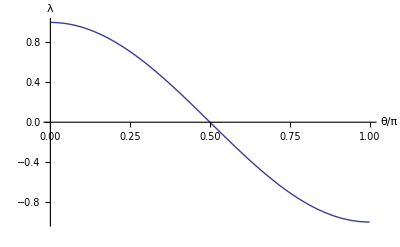

m1ffix.eps

```mathematica
Plot[Charm[Pi*theta],{theta,0,1},AxesLabel-> {"θ/π","λ"}]
Export["m1ffix.eps",%]
```

```mathematica
chartheta[x_,f_,theta_]=FullSimplify[CharEq[x,1,f*Cos[theta],f*Sin[theta]],{Element[x,Reals],Element[f,Reals],Element[theta,Reals]}]
```

```mathematica
chartheta_simple[x_,f_,theta_]=1/(12 f (-4+3 f^2))(2 f x (52-22 √(4-3 f^2)-24 x^2+3 f^2 (-13+6 x^2))+3 (-8 (-2+√(4-3 f^2)) (-5+2 x^2)+f^2 (60-17 √(4-3 f^2)+4 (-6+5 √(4-3 f^2)) x^2)) Cos[theta]-18 f (-4+3 f^2+2 √(4-3 f^2)) x Cos[2 theta]+3 (-3 f^2 (-4+√(4-3 f^2))+8 (-2+√(4-3 f^2))) Cos[3 theta])
```

```mathematica
Solve[chartheta_simple[x,0,0]==0,x,Element[x,Reals]]
```

```mathematica
ctterm1[f_,theta_]          =Simplify[chartheta[0,f,theta]]
cttermx2[x_,f_,theta_]=Simplify[(chartheta[x,f,theta]-ctterm1[f,theta])/x]
ctterm2[f_,theta_]          =Simplify[cttermx2[0,f,theta]]
cttermx3[x_,f_,theta_]=Simplify[(cttermx2[x,f,theta]-ctterm2[f,theta])/x]
ctterm3[f_,theta_]          =Simplify[cttermx3[0,f,theta]]
```

```mathematica
charthetamod[x_,f_,theta_]=Simplify[x^3+ctterm3[f,theta]*x^2+ctterm2[f,theta]*x+ctterm1[f,theta]]
```

```mathematica
Plot2D[{NSolve[charthetamod[x,f,theta]==0,x]},{f,-1,1},{theta,0,Pi}]
```

Plot2D[{{{x→1. Cos[theta]-(0.629961+1.09112 ⅈ) Cos[theta]^(1/3) (-0.5+1. Cos[theta]^2-0.5 Cos[2. theta])^(1/3)},{x→1. Cos[theta]-(0.629961-1.09112 ⅈ) Cos[theta]^(1/3) (-0.5+1. Cos[theta]^2-0.5 Cos[2. theta])^(1/3)},{x→1. Cos[theta]+1.25992 Cos[theta]^(1/3) (-0.5+1. Cos[theta]^2-0.5 Cos[2. theta])^(1/3)}}},{1,-1,1},{theta,0,π}]